argument:

Abs[⟨1|dH/dB|0⟩]/Δ^2 dB/dt<<1

∫Abs[⟨1|dH/dB|0⟩]/Δ^2 dB=∫dt

for two dimensions, this is replaced as

Abs[ ⟨1|dH/dB|0⟩dB +  ⟨1|dH/dA|0⟩dA]/Δ^2=dt

This is the local time cost

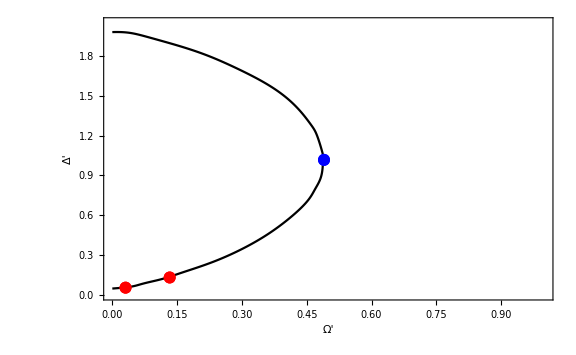
```mathematica
g1=-Graphics-;
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/junchenrong/Library/Mobile Documents/com~apple~CloudDocs/Research_projects/0.0 Rydberg_Atoms/adiabatic_ramping

```mathematica
(*curves={curve1,curve2,curve3,curve4,curve5};
DumpSave["curves.md",curves];*)
```

```mathematica
Clear[curves]
```

```mathematica
<<"curves.md"
```

```mathematica
g2=ListPlot[curves,PlotStyle->{Red,Green,Purple,LightRed,Blue},Joined->True,AspectRatio->3/2];
```

```mathematica
temp0="{{"~StringJoin~(Import["vectors.txt","String"]//StringReplace[#,"
"->"},{"]&)~StringJoin~"}}"//ToExpression;
temp0=temp0[[1;;Length[temp0]-1]];
```

```mathematica
Show[g2,g1,ListPlot[curvepart1~Join~curvepart2[1],PlotStyle->Red,Joined->True],ListPlot[{#[[1]]-0.005,#[[2]]-0.005}&/@(curvepart1~Join~curvepart2[2]),PlotStyle->Blue,Joined->True],ImageSize->Large,FrameLabel->{"Ω","Δ"},FrameStyle->{Directive[15],Directive[15]}]
```

```mathematica
g3=ListContourPlot[{#[[1]],#[[2]],#[[3]]}&/@temp0,Contours->20,PlotLegends->Automatic];
```

```mathematica
Show[g3,g1,g2,ListPlot[{{0,-1.6},{0,1}},PlotStyle->{Cyan,PointSize[0.03]}],PlotRange->{{0,2},{-2+0.04,1}},ImageSize->Large]
```

-Graphics-

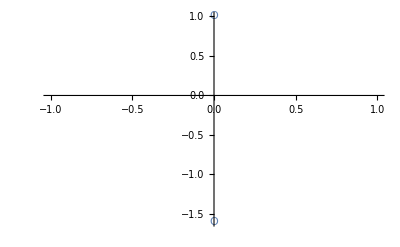

```mathematica
ListPlot[{{0,-1.6},{0,1}},PlotMarkers->"O"]
```

### The energy gap

```mathematica
temp0=Import["result"]//StringReplace[#,{"["->"{","]"->"}","e-5"->"*10^(-5)"}]&//ToExpression;
```

```mathematica
temp0=Select[temp0,Abs[#[[1]]]>0.0001&&Abs[#[[2]]]>0.0001&];
temp0={#[[1]],#[[2]],#[[3]],Abs[(#[[4]])/(#[[1]])],Abs[(#[[5]])/(#[[2]])]}&/@temp0;
```

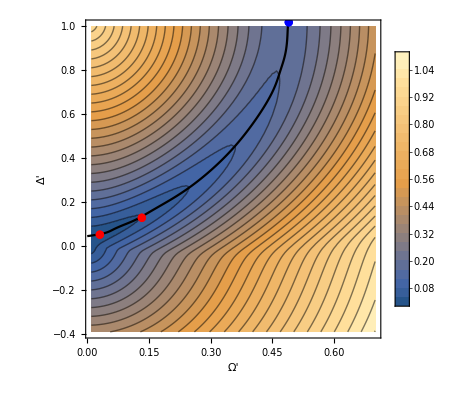

```mathematica
temp={#[[1]],#[[2]],#[[3]]}&/@temp0;
g2=Show[ListContourPlot[temp,PlotRange->{All,All,{0,2}},Contours->Table[0.04i,{i,1,40}],ContourShading->Automatic,FrameLabel->{"Ω'","Δ'"}(*Table[Darker[Cyan,i],{i,0,1,0.1}]*),PlotLegends->Automatic],g1]
```

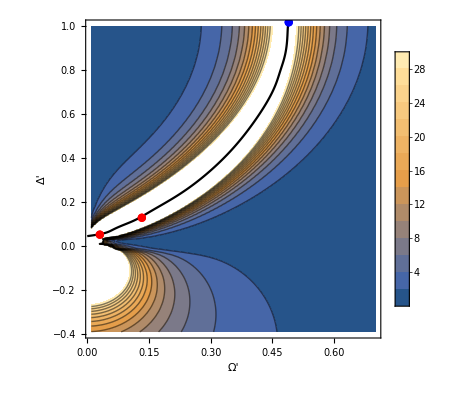

```mathematica
temp={#[[1]],#[[2]],Abs[#[[4]]]/(#[[3]])^2}&/@temp0;
Show[ListContourPlot[temp,PlotRange->{All,All,{0,30}},Contours->Table[2i,{i,1,20}],ContourShading->Automatic(*Table[Darker[Cyan,i],{i,0,1,0.1}]*),FrameLabel->{"Ω'","Δ'"},PlotLegends->Automatic],g1]
```

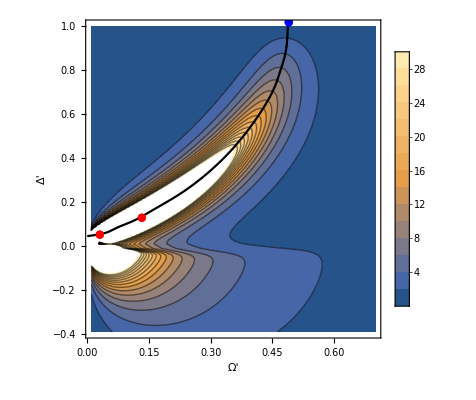

```mathematica
temp={#[[1]],#[[2]],Abs[#[[5]]]/(#[[3]])^2}&/@temp0;
Show[ListContourPlot[temp,PlotRange->{All,All,{0,30}},Contours->Table[2i,{i,1,40}],FrameLabel->{"Ω'","Δ'"},ContourShading->Automatic(*Table[Darker[Cyan,i],{i,0,1,0.1}]*),PlotLegends->Automatic],g1]
```

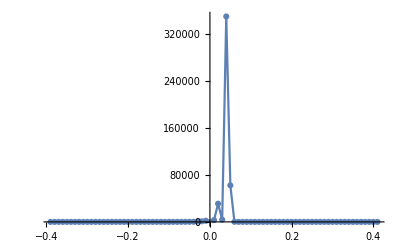

```mathematica
{#[[2]],Abs[#[[5]]]/(#[[3]])^2}&/@temp0[[1;;80]]//ListPlot[#,Joined->True,Mesh->All,PlotRange->All]&
```

```mathematica
Abs[#[[5]]]/(#[[3]])^2&/@temp0[[1;;80]]//Total
```

454320.

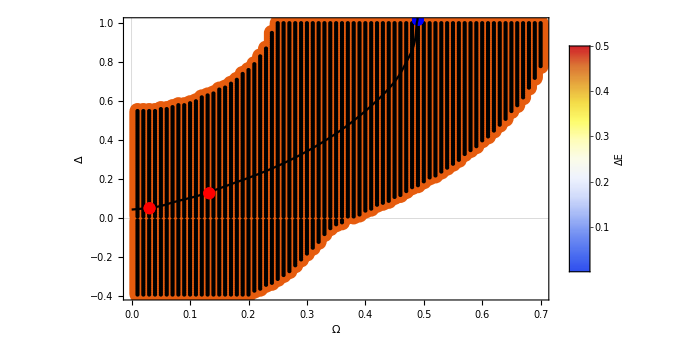

```mathematica
temp={#[[1]],#[[2]],#[[3]]}&/@temp0;
data=Sort[temp,#1[[3]]<#2[[3]]&];
data=Select[data,#[[3]]<0.5&];
(*2. Extract the minimum and maximum z-values to scale the color function*)
{zMin,zMax}=MinMax[data[[All,3]]](*{Min[data[[All,3]]],0.5}*);

(*3. Define your preferred color scheme*)
colorScheme="TemperatureMap"; (*Other good options:"TemperatureMap","Viridis"*)

(*4. Create the plot with a legend*)
Legended[ListPlot[(*Apply Style to each {x,y} coordinate using the z-value for color*)Style[{#1,#2},ColorData[{colorScheme,{zMin,zMax}}][#3]]&@@@data,PlotStyle->PointSize[0.02],(*Adjust point size as needed*)FrameStyle->Directive[20],Frame->True,Axes->False,PlotTheme->"Scientific",FrameLabel->{"Ω","Δ"},ImageSize->Large],(*Add the corresponding color bar*)BarLegend[{colorScheme,{zMin,zMax}},LegendLabel->"ΔE"]];
Show[g2,g1]
```

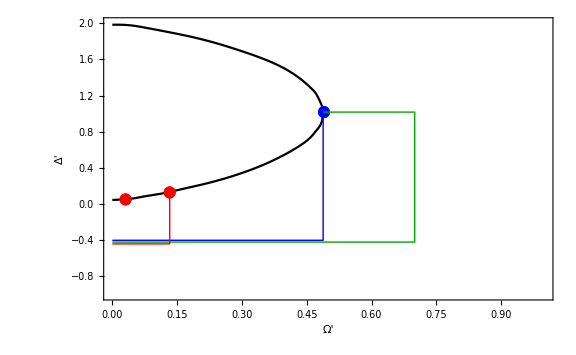

```mathematica
Show[Show[g1,PlotRange->{{0,1},{-1,2}}],Graphics[{Blue,Line[{{0,-0.4},{0.488,-0.4},{0.488,1.017}}]}],Graphics[{Darker[Green],Line[{{0,-0.42},{0.7,-0.42},{0.7,1.017},{0.488,1.017}}]}],Graphics[{Red,Line[{{0,-0.44},{0.13281,-0.44},{0.13281,0.139}}]}]]

(*Red=1456.829728895098,
Green=698.2629716987768,Blue=739.0010411507669*)
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/junchenrong/Library/Mobile Documents/com~apple~CloudDocs/Research_projects/0.0 Rydberg_Atoms/adiabatic_ramping

```mathematica
temp0="{{"~StringJoin~(Import["vectors.txt","String"]//StringReplace[#,"
"->"},{"]&)~StringJoin~"}}"//ToExpression;
temp0=temp0[[1;;Length[temp0]-1]];
```

```mathematica
g3=ListContourPlot[{#[[1]],#[[2]],#[[3]]}&/@temp0,Contours->20,PlotLegends->Automatic];
```

```mathematica
Show[g2,g1,ListPlot[curvepart1~Join~curvepart2[1],PlotStyle->Red,Joined->True],ListPlot[{#[[1]]-0.005,#[[2]]-0.005}&/@(curvepart1~Join~curvepart2[2]),PlotStyle->Blue,Joined->True],ImageSize->Large,FrameLabel->{"Ω","Δ"},FrameStyle->{Directive[15],Directive[15]}]
```

-Graphics-

```mathematica
Table[{0.002i,-3.2},{i,1,}]
```

```mathematica
Solve[{0.01*i,-4+0.01*j}=={2 0.06640515431,0.128825999371}]
```

```mathematica
-2+0.002*1520
```

1.04

```mathematica
0.002*1000
```

2.